# Cosmology Calculator

```mathematica
Clear["Global`*"];
pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

-Graphics-

```mathematica
(*scale factor in terms of the Redshift  *)
scalfactor[z_]:=1/(1+z);
redshift[a_]:=1/a-1;
```

-Graphics-

```mathematica
(*Function to compute conformal time for a given redshift*)
tau[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/(√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞},PrecisionGoal->12,AccuracyGoal->12]
```

-Graphics-

```mathematica
(*Function to compute Physical time for a given redshift = (a'(tau))/a*)
time[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/((1+z)√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞}]
```

Friedmann equation: (FROM https://en.wikipedia.org/wiki/Hubble%27s_law)

-Graphics-

```mathematica
(*Physical Hubble Function at a given redshift = (ȧ)/a *)
PhysicalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)
```

```mathematica
(*Conformal Hubble Function at a given redshift *)
ConformalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(1+3 w) +Ωm (1+z)+Ωr(1+z)^2)
```

```mathematica
(*Time derivative of the Conformal Hubble Function at a given redshift = (ȧ)/a *)
ConformalHubblePrime[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=D[ConformalHubble[z,H0,Ωm,Ωd,w,Ωr],z]*(-(1+z)^2)*ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]*1/(1+z);  (* (d HH)/dtau = dH/dz  dz/da da/dtau*)
```

```mathematica
D[ConformalHubble[z,H0,Ωm,Ωd,w,Ωr],z]
(*(*Physical Hubble Function at a given redshift = (ȧ)/a *)
ConformalHubblePrimePrime[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=D[ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr],z]*D[1/a-1,a]*ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]*1/(1+z);  (* (d ^2HH)/dtau^2 = dH/dz  dz/da da/dtau*)*)
```

(H0 ((1+3 w) (1+z)^(3 w) Ωd+Ωm+2 (1+z) Ωr))/(2 √((1+z)^(1+3 w) Ωd+(1+z) Ωm+(1+z)^2 Ωr))

```mathematica
(H0 ((1+3 w) (1+z)^(3 w) Ωd+Ωm+2 (1+z) Ωr))/(2 √((1+z)^(1+3 w) Ωd+(1+z) Ωm+(1+z)^2 Ωr))*ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]
```

1/2 H0^2 ((1+3 w) (1+z)^(3 w) Ωd+Ωm+2 (1+z) Ωr)

The equation to find a’’(\tau) which must be consistent with what we find previously. We don’t need to do it, instead we can just

Where for when we don’t have radiation:

-Graphics-

Here we neglect pressure from radiation, meaning that we don' t go deep to the radiation domination and we start our equations from z = 1000 for example

```mathematica
(*Here we neglect pressure from radiation, meaning that we don't go deep to the radiation domination and we start our equations from z=1000 for example*)

dNlnH[NN_,H0_,Ωm_,Ωd_,Ωr_,w_]:= D[ Log[ConformalHubble[1/E^NN-1,H0,Ωm,Ωd,w,Ωr]],NN](*N=ln a*)
Psiequation[ψ_,NN_,H0_,Ωm_,Ωd_,Ωr_,w_]:= ψ''[NN] +(3+ dNlnH[NN,H0,Ωm,Ωd,Ωr,w])ψ'[NN]+(2-(3 Ωm)/(2 Ωm + 2 Ωd Exp[-3w NN]+ 2 Ωr Exp[-NN])+dNlnH[NN,H0,Ωm,Ωd,Ωr,w])ψ[NN]
```

Finding Ψ fom the Growth factor equation

-Graphics--Graphics-

-Graphics-

```mathematica
Growthequation = DD''[τ] +a'[τ]/a[τ] DD'[τ]+-3/2 Ωm (a'[τ]/a[τ])^2 DD[τ];
```

Substituting the ansatz and then see if the equation we get is similar

```mathematica
Block[{DD},DD[τ_]:=Ψ[τ]a[τ];Growthequation]==0 /.{a'[τ]->Η[τ] a[τ]}/.{a''[τ]->Η'[τ]a[τ] + Η[τ]^2 a[τ]}//Simplify
```

a[τ] ((-4+3 Ωm) Η[τ]^2 Ψ[τ]-6 Η[τ] Ψ'[τ]-2 (Ψ[τ] Η'[τ]+Ψ''[τ]))==0

RESULTS

τ :  with high accuracy

```mathematica
(* Cosmology setting *)
H0=0.0691023;Ωm=0.31;Ωr=9 10^-5; w=-0.9;Ωd=1-Ωm -Ωr;
Clear["Ωm","Ωd","w","Ωr","H0"];
(*ConformalHubblePrime[0.0,H0,Ωm,Ωd,w,Ωr]*)
(*NumberForm[tau[1000,H0,Ωm,Ωd,w,Ωr],12]*)
(*Ωd*)
ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr]
Coefficient[ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr],Ωd]
```

-1/2 H0^2 (1+z) ((1+3 w) (1+z)^(3 w) Ωd+Ωm+2 (1+z) Ωr)

-1/2 H0^2 (1+3 w) (1+z)^(1+3 w)

```mathematica
-1/2 H0^2 (1+z) ((1+3 w) (1+z)^(3 w) Ωd+Ωm+2 (1+z) Ωr)//Simplify
```

-1/2 H0^2 (1+z) ((1+3 w) (1+z)^(3 w) Ωd+Ωm+2 (1+z) Ωr)

```mathematica
(*ss=D[H0 √(a[τ]^(1-3 w) Ωd +a[τ]Ωm +Ωr),τ]/a[τ]-(H0 (√(a[τ]^(1-3 w) Ωd +a[τ]Ωm +Ωr))/a[τ])^2/.a'[τ]->H0 √(a[τ]^(1-3 w) Ωd +a[τ]Ωm +Ωr)//Simplify*)
(*ss*)
(*ss[a,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.6899099999/.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/.w->-0.9/.a->1./(1000+1)*)
```

```mathematica
ss/.Ωd->0.6899099999/.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/.w->-0.9/.a[τ]->1./(106.75+1)
(*ss[a,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.6899099999/.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/.w->-0.9/.a->1./(1000+1)*)
```

ss

```mathematica
-1/2 Η0^2 a[τ]^(-1-3 w) ((-1+3 w) ΩDE a[τ]^(-1-3 w)+2 ΩDE a[τ]^2 a[τ]^(-1-3 w)-ΩM a[τ]^(3 w) a[τ]^(-1-3 w)+2 ΩR a[τ]^(1+3 w) a[τ]^(-1-3 w)+2 ΩM a[τ]^(2+3 w) a[τ]^(-1-3 w))//Expand
```

1/2 Η0^2 ΩDE a[τ]^(-2-6 w)-3/2 w Η0^2 ΩDE a[τ]^(-2-6 w)+1/2 Η0^2 ΩM a[τ]^(-2-3 w)-Η0^2 ΩR a[τ]^(-1-3 w)-Η0^2 ΩDE a[τ]^(-6 w)-Η0^2 ΩM a[τ]^(-3 w)

```mathematica
a[τ]
```

a message Type

```mathematica
ss
```

ss

```mathematica
ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.6899099999/.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/.w->-0.9/.z->106.75
```

-0.0847392

```mathematica
ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.6899099999/.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/.w->-0.9/.z->0
```

0.00205967

=

```mathematica
(* Cosmology setting *)
Ωd=0.687;H0=0.0691023;Ωm=0.31;Ωr=9 10^-5; w=-0.9;
Clear["Ωm","Ωd","w","Ωr","H0"];
LogLinearPlot[tau[z,H0,Ωm,Ωd,w,Ωr],{z,0,40},ImageSize->Large,PlotRange->All,AxesLabel->{"z","τ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

NIntegrate::inumr: The integrand 1/(H0 √((1+z)^(3 (1+w)) Ωd+(1+z)^3 Ωm+(1+z)^4 Ωr)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.039068}}.

NIntegrate::inumr: The integrand 1/(H0 √(1.03907^(3. (1.+w)) Ωd+1.12184 Ωm+1.16567 Ωr)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.039068}}.

NIntegrate::inumr: The integrand 1/(H0 √((1+z)^(3 (1+w)) Ωd+(1+z)^3 Ωm+(1+z)^4 Ωr)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.0450045}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

The formula for \HH(z)

-Graphics-

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]//pdConv
```

H0 √(Ωd (z+1)^(3 w+1)+Ωm (z+1)+Ωr (z+1)^2)

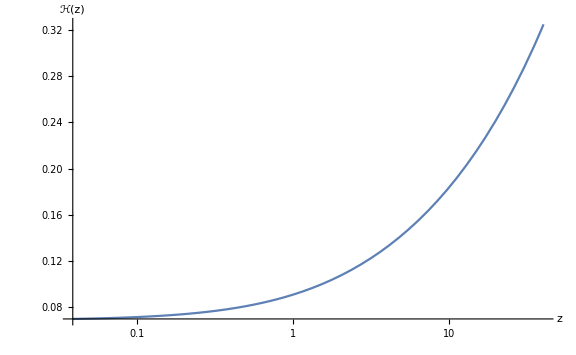

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Eq=ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-0.1;
LogLinearPlot[Eq,{z,0,40},ImageSize->Large,AxesLabel->{"z","ℋ(z)"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

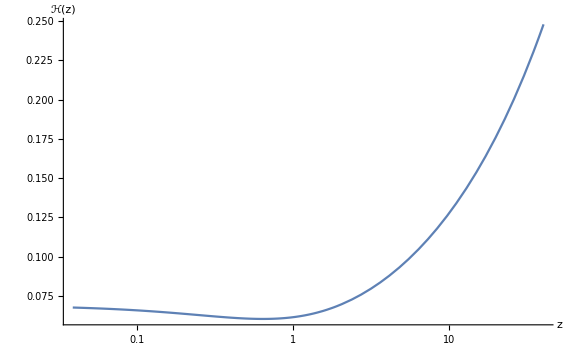

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Eq=ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1;
LogLinearPlot[Eq,{z,0,40},ImageSize->Large,PlotRange->All,AxesLabel->{"z","ℋ(z)"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

The formula for d \HH/dtau (z)

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr]//pdConv
```

ConformalHubblePrime(z,H0,Ωm,Ωd,w,Ωr)

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Eq=ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1;
LogLinearPlot[Eq,{z,0,200},ImageSize->Large,PlotRange->All,AxesLabel->{"z","ℋ'(z)"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

-Graphics-

The formula for Ψ

Psiequation[ψ_,NN_,H0_,Ωm_,Ωd_,Ωr_,w_]:= ψ''[NN] +(3+ dNlnH[NN,H0,Ωm,Ωd,Ωr,w])ψ'[NN]+(2-(3 Ωm)/(2 Ωm + 2 Ωd Exp[-3w NN]+ 2 Ωr Exp[-NN])+dNlnH[NN,H0,Ωm,Ωd,Ωr,w])ψ[NN]

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Sol = DSolve[(Psiequation[ψ,NN,H0,Ωm,Ωd,Ωr,w]==0),ψ[NN], NN];
Print[Sol];
```

DSolve[(2+(-(ⅇ^-NN)^(1+3 w) (1+3 w) Ωd-ⅇ^-NN Ωm-2 ⅇ^(-2 NN) Ωr)/(2 ((ⅇ^-NN)^(1+3 w) Ωd+ⅇ^-NN Ωm+ⅇ^(-2 NN) Ωr))-(3 Ωm)/(2 ⅇ^(-3 NN w) Ωd+2 Ωm+2 ⅇ^-NN Ωr)) ψ[NN]+(3+(-(ⅇ^-NN)^(1+3 w) (1+3 w) Ωd-ⅇ^-NN Ωm-2 ⅇ^(-2 NN) Ωr)/(2 ((ⅇ^-NN)^(1+3 w) Ωd+ⅇ^-NN Ωm+ⅇ^(-2 NN) Ωr))) ψ'[NN]+ψ''[NN]==0,ψ[NN],NN]

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Plot[ψ[NN]/.Sol/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1/.C[1]->10^-5/.C[2]->0,{NN,Log[1/(1+1000)],Log[1/(1+0)]},ImageSize->Large,PlotRange->All,AxesLabel->{"Ln(a)","Ψ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

DSolve::dsvar: -6.90861 cannot be used as a variable.

ReplaceAll::reps: {DSolve[(2-3 Ωm Power[«2»]+1/2 Plus[«3»] Power[«2»]) ψ[-6.90861]+(3+1/2 Plus[«3»] Power[«2»]) ψ'[-6.90861]+ψ''[-6.90861]==0,ψ[-6.90861],-6.90861]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::dsvar: -6.90861 cannot be used as a variable.

ReplaceAll::reps: {DSolve[(2-3 Ωm Power[«2»]+1/2 Plus[«3»] Power[«2»]) ψ[-6.90861]+(3+1/2 Plus[«3»] Power[«2»]) ψ'[-6.90861]+ψ''[-6.90861]==0,ψ[-6.90861],-6.90861]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::dsvar: -6.90861 cannot be used as a variable.

General::stop: Further output of DSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {DSolve[(2-0.93 Power[«2»]+1/2 Plus[«3»] Power[«2»]) ψ[-6.90861]+(3+1/2 Plus[«3»] Power[«2»]) ψ'[-6.90861]+ψ''[-6.90861]==0,ψ[-6.90861],-6.90861]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Log[1/(1+1000)]//N
```

-6.90875

Numerical solution of Ψ

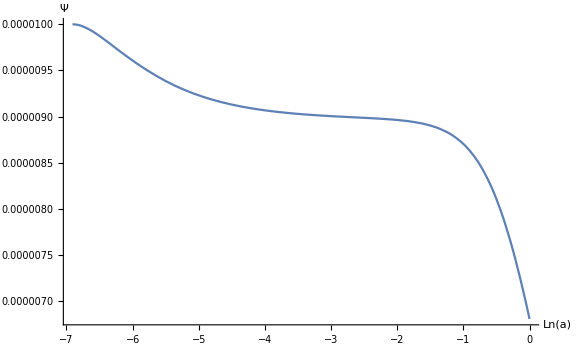

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Solnumer = NDSolve[{(Psiequation[ψ,NN,H0,Ωm,Ωd,Ωr,w]==0)/.Ωd->0.6872344 /.H0->0.0691023/.Ωm->0.3/.Ωr->9 10^-5/. w->-0.9,ψ[Log[1/(1+1000)]]==10^-5,ψ'[Log[1/(1+1000)]]==0},ψ,{NN,Log[1/(1+1000)],Log[1/(1+0)]}];
Plot[ψ[NN]/.Solnumer,{NN,Log[1/(1+1000)],Log[1/(1+0)]},ImageSize->Large,PlotRange->{10^-5,0},AxesLabel->{"Ln(a)","Ψ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

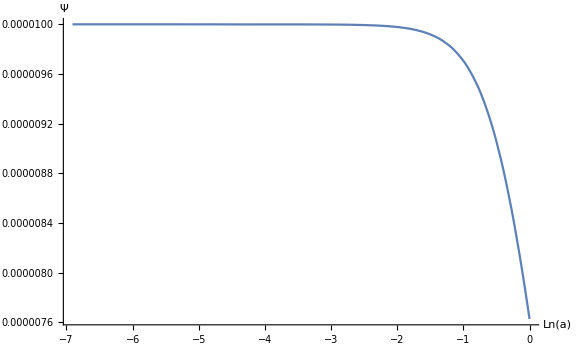

```mathematica
Solnumer = NDSolve[{(Psiequation[ψ,NN,H0,Ωm,Ωd,0,w]==0)/.Ωd->0.6872344 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-0.9,ψ[Log[1/(1+1000)]]==10^-5,ψ'[Log[1/(1+1000)]]==0},ψ,{NN,Log[1/(1+1000)],Log[1/(1+0)]}];
Plot[ψ[NN]/.Solnumer,{NN,Log[1/(1+1000)],Log[1/(1+0)]},ImageSize->Large,PlotRange->All,AxesLabel->{"Ln(a)","Ψ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

```mathematica
1-0.31-9 10^-5
```

0.68991

```mathematica
Solnumer = NDSolve[{(Psiequation[ψ,NN,H0,Ωm,Ωd,Ωr,w]==0)/.Ωd->0.6899099999999999 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-0.9,ψ[Log[1/(1+1000)]]==10^-5,ψ'[Log[1/(1+1000)]]==0},ψ,{NN,Log[1/(1+1000)],Log[1/(1+0)]},AccuracyGoal -> 18,PrecisionGoal -> 20];
ψ[NN]/.Solnumer/.NN->-2.8090319197037221 10^-3
```

{6.88006×10^-6}

6.8800565058

```mathematica
{8.749562185339175*^-6}
8.7495835461812425
```

Checking whether at high z (early times) H(τ) behaves like 2/τ as expected

(to be discussed by FH)

```mathematica
Ωm= 3/10;ΩR = 0;w=-1;H0= 0.06927345697102467;
s = NDSolve[{(a'[tau] -a[tau]H0 √(ΩR a[tau]^-2 + Ωm a[tau]^-1+(1-Ωm)a[tau]^(-(1+3 w)))== 0),a[46]==1},a, {tau,0.01,46.3},Method->"ExplicitRungeKutta"]
```

{{a→InterpolatingFunction[…]}}

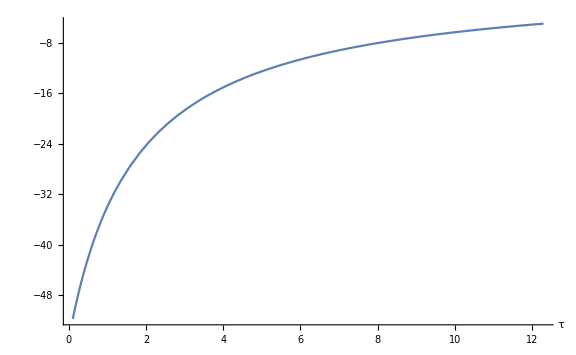

```mathematica
Plot[Evaluate[((a'[t]/.s)/(a[t]/.s))*(t-47)],{t,0.1,12.3},ImageSize->Large,PlotRange->All,AxesLabel->{"τ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

```mathematica
Ωm= 1;ΩR = 0;w=-1;H0= 0.06927345697102467;
s = NDSolve[{(a'[tau] -a[tau]^(-1/2)== 0),a[16]==1},a, {tau,0.0,12.3}]
```

{{a→InterpolatingFunction[…]}}

```mathematica
Ωm= 1;ΩR = 0;w=-1;H0= 0.06927345697102467;
news = DSolve[(a'[tau] -a[tau]^(-1/2)== 0),a, tau]
```

{{a→Function[{tau},(3/2)^(2/3) (tau+C[1])^(2/3)]}}

```mathematica
{{a->Function[{tau},(3/2)^(2/3) (tau+C[1])^(2/3)]}}
```

```mathematica
Solve[(3/2)^(2/3) (47+c)^(2/3)==1,c]//N
a'[t]/.news
```

{{c→-46.3333}}

{(2/3)^(1/3)/(t+C[1])^(1/3)}

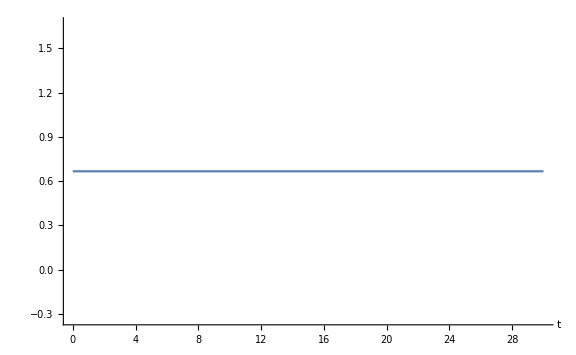

```mathematica
Plot[Evaluate[(((a'[t]/.news)/(a[t]/.news))/.C[1]->-46.333333333333336)*(t-46.333333333333336)],{t,0.0,30},ImageSize->Large,PlotRange->All,AxesLabel->{"t"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

```mathematica
Plot[Evaluate[((a'[t]/.news)/(a[t]/.news))*(t-47)],{t,0.1,12.3},ImageSize->Large,PlotRange->All,AxesLabel->{"τ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

-Graphics-

```mathematica
Ωm= 1;ΩR = 0;w=-1;H0= 0.06927345697102467;
news = NDSolve[{(a'[tau] -a[tau]^(-1/2)== 0),a[47]==1},a, {tau,0.0,46.3}]
```

{{a→InterpolatingFunction[…]}}

```mathematica
Plot[a[tau]/.news,{tau,0.1,10.3},ImageSize->Large,PlotRange->All,AxesLabel->{"τ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

-Graphics-

```mathematica
Plot[Evaluate[((a'[tau]/.news)/(a[tau]/.news))],{tau,0.0,12.3},ImageSize->Large,PlotRange->All,AxesLabel->{"τ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

-Graphics-